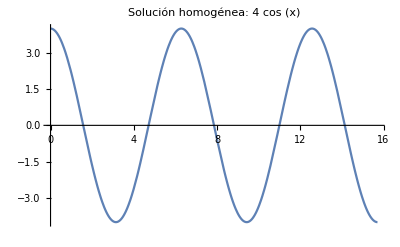

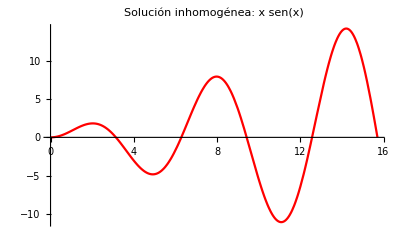

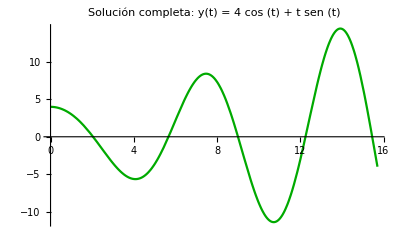

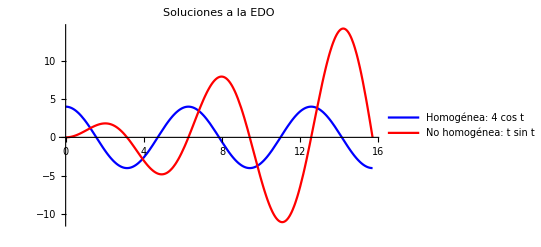

```mathematica
Plot[4 Cos [x], {x,0, 5 Pi}, PlotLabel->Style["Solución homogénea: 4 cos (x)", FontSize->14, Black]]
Plot[x Sin [x], {x, 0, 5 Pi}, PlotLabel->Style["Solución inhomogénea: x sen(x)", FontSize->14, Black], PlotStyle->Red]
Plot[4 Cos[x] + x Sin [x],{x,0,5 Pi}, PlotLabel->Style["Solución completa: y(t) = 4 cos (t) + t sen (t)", Black, FontSize->14], PlotStyle->Darker[Green]]
Plot[{4 Cos[x], x Sin[x]},{x,0, 5 Pi}, PlotLegends->{"Homogénea: 4 cos t", "No homogénea: t sin t"}, PlotLabel->Style["Soluciones a la EDO", Black, FontSize->14], PlotStyle->{Blue, Red}]
```